## Pregunta 3

```mathematica
$ContextPath
```

{FindRoots`,NumericalFunctions`,CPUArithmetic`,Interpolation`,Functions`,System`,Global`}

#### Funcion definida utilizando reglas de transformacion globales

```mathematica
globaltransformF/@Range[0.5,3.5]//RepeatedTiming
```

{0.0000298813,{0.0208333,0.479167,0.479167,0.0208333}}

#### Funcion definida utilizando reglas de transformacion locales

```mathematica
localtransformF/@Range[0.5,3.5]//RepeatedTiming
```

{0.0000953191,{0.0208333,0.479167,0.479167,0.0208333}}

#### Funcion definida utilizando programacion estructurada

```mathematica
structuredF/@Range[0.5,3.5]//RepeatedTiming
```

{0.0000236774,{0.0208333,0.479167,0.479167,0.0208333}}

#### Funcion definida utilizando la funcion Piecewise

```mathematica
piecewiseF/@Range[0.5,3.5]//RepeatedTiming
```

{0.0000272645,{0.0208333,0.479167,0.479167,0.0208333}}

## Pregunta 4

#### Coeficientes de Legendre utilizando algoritmo recursivo

```mathematica
legendreCoefficientesR[20]//RepeatedTiming
```

{1.10898×10^-7,{46189/262144,0,-4849845/131072,0,334639305/262144,0,-557732175/32768,0,15058768725/131072,0,-29113619535/65536,0,136745788725/131072,0,-49589132175/32768,0,347123925225/262144,0,-83945001525/131072,0,34461632205/262144}}

#### Coeficientes de Legendre utilizando algoritmo estructurado

```mathematica
legendreCoefficientesS[20]//RepeatedTiming
```

{0.000313228,{46189/262144,0,-4849845/131072,0,334639305/262144,0,-557732175/32768,0,15058768725/131072,0,-29113619535/65536,0,136745788725/131072,0,-49589132175/32768,0,347123925225/262144,0,-83945001525/131072,0,34461632205/262144}}

#### Coeficientes de Legendre utilizando algoritmos internos de Mathematica

```mathematica
CoefficientList[LegendreP[20,x],x]//RepeatedTiming
```

{0.00342687,{46189/262144,0,-4849845/131072,0,334639305/262144,0,-557732175/32768,0,15058768725/131072,0,-29113619535/65536,0,136745788725/131072,0,-49589132175/32768,0,347123925225/262144,0,-83945001525/131072,0,34461632205/262144}}

# Pregunta 4 Tarea 3

```mathematica
<<Notation`
```

```mathematica
Notation[Subscript[ℍ, v_][z_] ⟺ struveH[v_,z_]]
```

```mathematica
Subscript[ℍ, 1/2][4]
```

0.659708

```mathematica
Subscript[ℍ, 3/2][5]
```

1.28535

```mathematica
Subscript[ℍ, -1/2][4.]
```

-0.301921

```mathematica
struveH[-1/2,4.]
```

-0.301921

```mathematica
StruveH[-1/2,4.]
```

-0.301921

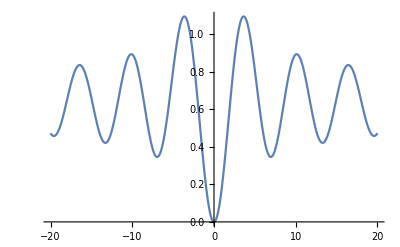

```mathematica
Plot[ℍ_1.[z],{z,-20,20}]
```